# Compatibility Equations

## Equation 1

The first equation explores using the Gausian function in 2 dimentions as a means by which compatibility coefficients in the middle range get more emphasis than those at the low and high ends.

```mathematica
y = c1 1/(σ √(2π))ⅇ^(-(x-μ)^2/(2c2(σ)^2))
```

0.997356 ⅇ^(-50. (-0.5+x)^2)

```mathematica
c1=.5
c2=.25
σ=.2
μ=.5
```

0.5

0.25

0.2

0.5

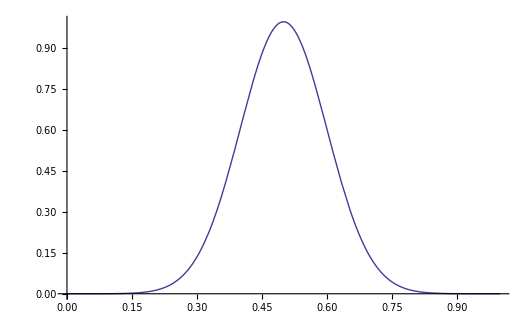

```mathematica
Plot[y, {x, -0, 1.}]
```

## Equation 2

This equation explores using an arctangent as a means by which compatibility coefficients in below middle range get less emphasis than those at  the high end.

```mathematica
y=π/4 ArcTan[π*x]*x
```

1/4 π x ArcTan[π x]

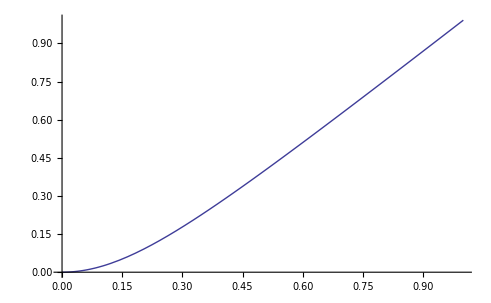

```mathematica
Plot[y, {x, -0, 1}]
```

## Equation 3

This equation explores using the inverse of the Gausian function in 2 dimentions as a means by which compatibility coefficients in the upper and lower ranges get more emphasis than those in the middle.

```mathematica
y = 1 - c1 1/(σ √(2π))ⅇ^(-(x-μ)^2/(2c2(σ)^2))
```

1-(c1 ⅇ^(-(x-μ)^2/(2 c2 σ^2)))/(√(2 π) σ)

```mathematica
c1=.5
c2=.25
σ=.2
μ=.5
```

0.5

0.25

0.2

0.5

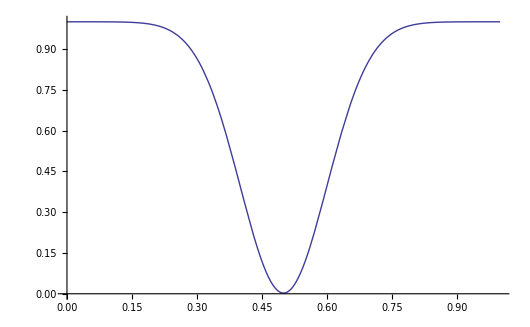

```mathematica
Plot[y, {x, -0, 1.}]
```